## Load program

```mathematica
<<"/Users/kouamano/gitsrc/MATH_SCRIPT/SCRIPTS/pointlisttolines.txt"
```

## Program

```mathematica
maxOrderNum=200;
```

```mathematica
pointListToLines[pointList_,neighbothoodSize_:6]:=Module[{L=DeleteDuplicates[pointList],NF,lambda,lineBag,counter,seenQ,sLB,nearest,nearest1,nextPoint,couldReverseQ,d,n,s},NF=Nearest[L];
lambda=Length[L];
Monitor[(*list of segments*)lineBag={};
counter=0;
While[counter<lambda,(*new segment*)sLB={RandomChoice[DeleteCases[L,_?seenQ]]};
seenQ[sLB[[1]]]=True;
counter++;
couldReverseQ=True;
(*complete segment*)While[(nearest=NF[Last[sLB],{Infinity,neighbothoodSize}];
nearest1=SortBy[DeleteCases[nearest,_?seenQ],1. EuclideanDistance[Last[sLB],#]&];
nearest1=!={}||couldReverseQ),If[nearest1==={},(*extend the other end;penalize sharp edges*)sLB=Reverse[sLB];
couldReverseQ=False,(*prefer straight continuation*)nextPoint=If[Length[sLB]≤3,nearest1[[1]],d=1. Normalize[(sLB[[-1]]-sLB[[-2]])+1/2 (sLB[[-2]]-sLB[[-3]])];
n={-1,1} Reverse[d];
s=Sort[{Sqrt[(d.(#-sLB[[-1]]))^2+(*perpendicular*)2 (n.(#-sLB[[-1]]))^2],#}&/@nearest1];
s[[1,2]]];
AppendTo[sLB,nextPoint];
seenQ[nextPoint]=True;
counter++]];
AppendTo[lineBag,sLB]];
(*return segments sorted by length*)Reverse[SortBy[Select[lineBag,Length[#]>12&],Length]],(*monitor progress*)Grid[{{Text[Style["progress point joining",Darker[Green,0.66]]],ProgressIndicator[counter/lambda]},{Text[Style["number of segments",Darker[Green,0.66]]],Length[lineBag]+1}},Alignment->Left,Dividers->Center]]]
```

```mathematica
fourierComponentData[pointList_,nMax_,op_]:=Module[{epsilon=10^-3,myu=2^14,M=10000,s,scale,delta,L,nds,sMax,if,xyFunction,X,Y,XFT,YFT,type},(*prepare curve*)scale=1. Mean[Table[Max[fl/@pointList]-Min[fl/@pointList],{fl,{First,Last}}]];
delta=EuclideanDistance[First[pointList],Last[pointList]];
L=Which[op==="Closed",type="Closed";
If[First[pointList]===Last[pointList],pointList,Append[pointList,First[pointList]]],op==="Open",type="Open";
pointList,delta==0.,type="Closed";
pointList,delta/scale<op,type="Closed";
Append[pointList,First[pointList]],True,type="Open";
Join[pointList,Rest[Reverse[pointList]]]];
(*re-parametrize curve by arclength*)xyFunction=BSplineFunction[L,SplineDegree->4];
nds=NDSolve[{s'[t]==Sqrt[xyFunction'[t].xyFunction'[t]],s[0]==0},s,{t,0,1},MaxSteps->10^5,PrecisionGoal->4];
(*total curve length*)sMax=s[1]/.nds[[1]];
if=Interpolation[Table[{s[rho]/.nds[[1]],rho},{rho,0,1,1/M}]];
X[t_Real]:=BSplineFunction[L][Max[Min[1,if[(t+Pi)/(2 Pi) sMax]],0]][[1]];
Y[t_Real]:=BSplineFunction[L][Max[Min[1,if[(t+Pi)/(2 Pi) sMax]],0]][[2]];
(*extract Fourier coefficients*){XFT,YFT}=Fourier[Table[#[N@t],{t,-Pi+epsilon,Pi-epsilon,(2 Pi-2 epsilon)/myu}]]&/@{X,Y};
{type,2 Pi/Sqrt[myu]*((Transpose[Table[{Re[#],Im[#]}&[Exp[I k Pi] #[[k+1]]],{k,0,nMax}]]&/@{XFT,YFT}))}]
Options[fourierComponents]={"MaxOrder"->maxOrderNum,"OpenClose"->0.025};
```

```mathematica
fourierComponents[pointLists_,OptionsPattern[]]:=Monitor[Table[fourierComponentData[pointLists[[k]],If[Head[#]===List,#[[k]],#]&[OptionValue["MaxOrder"]],If[Head[#]===List,#[[k]],#]&[OptionValue["OpenClose"]]],{k,Length[pointLists]}],Grid[{{Text[Style["progress calculating Fourier coefficients",Darker[Green,0.66]]],ProgressIndicator[k/Length[pointLists]]}},Alignment->Left,Dividers->Center]]/;Depth[pointLists]===4
```

```mathematica
makeFourierSeries[{"Closed"|"Open",{{cax_,sax_},{cay_,say_}}},t_,n_]:={Sum[If[k==0,1/2,1] cax[[k+1]] Cos[k t]+sax[[k+1]] Sin[k t],{k,0,Min[n,Length[cax]]}],Sum[If[k==0,1/2,1] cay[[k+1]] Cos[k t]+say[[k+1]] Sin[k t],{k,0,Min[n,Length[cay]]}]}
```

```mathematica
paraplot[n_]:=Show[{ParametricPlot[Evaluate[makeFourierSeries[#,t,n]&/@fCs],{t,-Pi,Pi},Axes->False](*,Graphics[Text[Style["n="<>ToString[n],Large,Bold],Scaled[{.9,.1}]]]*)}(*,ImageSize->{500,500}*)]
```

## Execution

```mathematica
file="/Users/kouamano/gitsrc/Kenkyu-kai/Mathematica_Kenkyu-kai/about-miku.jpg"
```

/Users/kouamano/gitsrc/Kenkyu-kai/Mathematica_Kenkyu-kai/about-miku.jpg

```mathematica
img=Import[file];
```

```mathematica
edgeImage=Thinning[EdgeDetect[ColorConvert[ImagePad[Image[Map[Most,ImageData[img],{2}]],20,White],"Grayscale"]]]
```

-Graphics-

```mathematica
ImageData[edgeImage]
```

{1}
 |  |  |  |

```mathematica
Position[ImageData[edgeImage],1,{2}]
```

{{61,433},{62,426},{62,428},{62,432},{62,434},{63,425},{63,428},{63,431},{63,435},{63,436},{64,424},{64,427},{64,430},29828,{918,708},{918,709},{919,168},{919,170},{919,171},{919,269},{919,272},{919,281},{919,568},{919,597},{920,169},{920,270},{920,271}}
 |  |  |  |

```mathematica
edgePoints={#2,-#1}&@@@Position[ImageData[edgeImage],1,{2}];
```

```mathematica
SeedRandom[2];
hLines=pointListToLines[edgePoints,16];
```

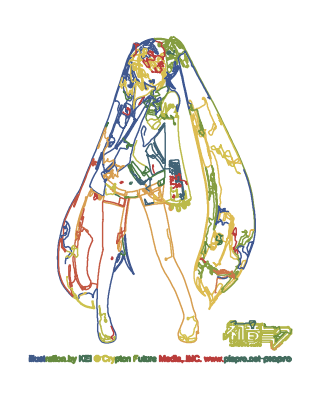

```mathematica
Graphics[{ColorData["DarkRainbow"][RandomReal[]],Line[#]}&/@hLines]
```

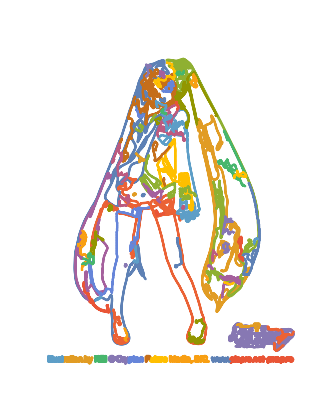

```mathematica
fCs=fourierComponents[hLines];
Show[ParametricPlot[Evaluate[makeFourierSeries[#,t,200]&/@fCs],{t,-Pi,Pi},Axes->False]]
```

```mathematica
Partition[Table[paraplot[n],{n,1,200,20}],4]//GraphicsGrid
```

-Graphics-

```mathematica
curves=makeFourierSeries[#,t,200]&/@fCs;
```

```mathematica
Style[Map[Short,Rationalize[curves,0.002]],16]
```

{{«605»+1/14 Sin[199 t]+10/19 Sin[200 t],«1»},{«597»+4/31 Sin[199 t]-5/18 Sin[200 t],-34822/21+«587»},{17814/11+«605»+11/20 Sin[199 t]+11/17 Sin[200 t],«1»},{11922/11+«572»+8/19 Sin[199 t]+17/30 Sin[200 t],-50391/29+«601»+17/52 «1»},{26305/13+(1039 Cos[t])/7+«615»+3/13 Sin[200 t],-39878/15+«587»},{«603»+2/11 Sin[200 t],-14465/29-(2096 «1»)/27+«599»},{«1»,-15764/13+(3186 Cos[t])/7+«574»+7/26 Sin[199 t]-17/35 Sin[200 t]},{50993/39-(1501 Cos[t])/16+«594»+1/22 Sin[199 t]+5/34 Sin[200 t],«1»},{11659/21+(557 Cos[t])/24+«602»,-42750/23-(«1»)/14+«576»},{21217/15-(1363 Cos[t])/15+«586»+1/51 Sin[199 t]-1/98 Sin[200 t],«1»},{22522/11-(5959 Cos[t])/26+«602»+3/26 Sin[200 t],«1»},{6173/8+«598»+1/89 Sin[200 t],-18877/10+«589»+1/9 Sin[200 t]},{11255/8-(2990 Cos[t])/21+«599»+1/13 Sin[199 t]-1/51 Sin[200 t],-(«5»)/9+«592»},{79297/64-(437 Cos[t])/9+«571»+1/21 Sin[199 t]+1/11 Sin[200 t],-(«5»)/23+«638»},{«1»,-35673/32-(2215 Cos[t])/17+«605»+1/167 Sin[199 t]-1/64 Sin[200 t]},{25704/13-(703 Cos[t])/28+«584»+1/15 Sin[199 t]-1/126 Sin[200 t],«1»},{6781/16-(1511 Cos[t])/16+«582»+1/21 Sin[199 t]+1/16 Sin[200 t],«1»},{56317/50-(2326 Cos[t])/17+«597»,-34373/26+«556»+1/111 Sin[200 t]},{18135/23+(817 Cos[t])/35+«587»+1/42 Sin[199 t]+1/169 Sin[200 t],«1»},{10145/13-(2137 Cos[t])/31+«600»+1/77 Sin[199 t]-1/23 Sin[200 t],«1»},{16570/19-(761 Cos[t])/24+«584»+1/26 Sin[198 t]+1/321 Sin[199 t],«1»},{9617/42-(1081 Cos[t])/21+«573»,-185412/65+«590»+1/49 Sin[200 t]},{30884/27-(929 Cos[t])/25+«566»+1/179 Sin[198 t]-1/39 Sin[200 t],«1»},{«536»+1/64 Sin[199 t]+1/74 Sin[200 t],-28129/13+«573»+1/147 Sin[200 t]},{19309/13+(804 Cos[t])/29+«535»+1/101 Sin[198 t]+1/159 Sin[199 t],«1»},{5887/10+«571»+1/208 Sin[199 t]-1/159 Sin[200 t],«540»+1/222 «1»},{65591/70-(1123 Cos[t])/22+«574»,«561»+1/56 Sin[198 t]},{«576»+«1»-1/64 Sin[199 t]-1/47 Sin[200 t],-20483/11+«544»+1/78 Sin[200 t]},{15135/19+«557»+1/69 Sin[199 t]-1/92 Sin[200 t],«1»},{11965/19+(1574 Cos[t])/43+«584»+1/48 Sin[199 t],-54124/19+«577»},{«536»+1/140 Sin[198 t]-1/201 Sin[200 t],-97089/34+«485»+1/140 Sin[200 t]},{28115/18+«555»+1/179 Sin[198 t]-1/163 Sin[199 t],«1»},{36011/26-(139 Cos[t])/8+«521»,«1»},{«565»+«1»+1/59 Sin[199 t]+1/62 Sin[200 t],-36919/14+«564»+1/256 Sin[«1»]},{28035/16+(29 Cos[t])/14+«594»+1/86 Sin[199 t]+1/43 Sin[200 t],-(«5»)/27+«575»},{21654/19-(587 Cos[t])/12+«387»+1/367 Sin[149 t]-1/453 Sin[177 t],«1»},{«610»+1/181 Sin[199 t],-4918/7+(3997 «1»)/37+«538»},{«530»+1/237 Sin[199 t],-3919/11-(1111 «1»)/15+«488»+1/(«3») «1»+1/465 Sin[200 t]},{«569»+1/75 Sin[199 t]+1/201 Sin[200 t],-164993/119+«559»+1/103 Sin[200 t]},{6979/12+(686 Cos[t])/29+«576»+1/115 Sin[199 t]+1/461 Sin[200 t],«1»},{50485/27+«487»+1/420 Sin[194 t]-1/235 Sin[198 t],«532»+1/(«3») «1»},{38383/31+«534»+1/321 Sin[200 t],-5818/13+«498»},{18994/13-(173 Cos[t])/19+«499»+1/244 Sin[199 t],-2375/6+«538»},{17753/21+«411»+1/469 Sin[147 t]-1/444 Sin[159 t],-27529/19+«398»+1/(«3») «1»},{12126/23+«473»,-82807/42+«429»+1/239 Sin[196 t]},{25126/19+«454»,-24984/13+«403»+1/311 Sin[156 t]},{29456/15+«501»+1/337 Sin[180 t]-1/264 Sin[199 t],«472»+1/(«3») «1»},{27433/26-(304 Cos[t])/11+«307»+1/441 Sin[108 t]+1/470 Sin[109 t],«1»},{30759/25-(319 Cos[t])/10+«484»,-19898/13+«481»+1/291 Sin[200 t]},{48667/28+«504»+1/484 Sin[199 t]+1/492 Sin[200 t],-61673/33+«487»+1/(«3») «1»},«1»,{15113/16+«251»+1/458 Sin[69 t]+1/420 Sin[70 t],«1»},{50233/27+«432»+1/456 Sin[195 t],-12221/10+«483»},{36573/31-(332 Cos[t])/35+«352»+1/355 Sin[127 t]+1/369 Sin[137 t],«1»},{12184/17-(106 Cos[t])/27+«340»+1/453 Sin[62 t],-25759/17+«376»+1/449 Sin[«1»]},{28663/25+«488»+1/182 Sin[197 t]-1/192 Sin[199 t],«1»},{49114/49-(892 Cos[t])/21+«219»+1/460 Sin[127 t]+1/488 Sin[128 t],«1»},{«1»,-29050/11+(525 Cos[t])/11+«225»},{17937/11-(755 Cos[t])/54+«282»+1/290 Sin[69 t],«301»+1/467 Sin[«1»]},{31925/24+(655 Cos[t])/31+«179»+1/442 Sin[45 t]-1/325 Sin[47 t],«1»},{«292»+1/458 Sin[108 t]+1/463 Sin[111 t],«1»},{16673/17+«329»,-13997/13-(540 «1»)/19+«324»+1/389 Sin[«1»]+1/406 Sin[135 t]},{55718/57+«282»+1/367 Sin[61 t],-15376/19+«308»+1/482 Sin[81 t]},{41804/19-(1447 Cos[t])/36+«221»+1/365 Sin[19 t]+1/415 Sin[23 t],«1»},{30436/29+«234»+1/452 Sin[97 t]+1/379 Sin[112 t],«1»},{36973/31-(77 Cos[t])/16+«219»+1/434 Sin[90 t]+1/495 Sin[91 t],-(«5»)/18+«248»},{33994/17+(119 Cos[t])/9+«290»+1/470 Sin[165 t]+1/435 Sin[166 t],«1»},{24677/14+(860 Cos[t])/23+«143»,«119»+1/406 Sin[19 t]},{33643/21+(344 Cos[t])/21+«227»+1/280 Sin[25 t]+1/342 Sin[26 t],«1»},{12503/11+(247 Cos[t])/25+«330»+1/492 Sin[191 t],-11891/16+«379»+1/472 Sin[«1»]},{24830/19+«88»,«208»+1/471 Sin[33 t]+1/453 Sin[34 t]},{9747/10-(669 Cos[t])/23+«188»,-14386/21+«273»+1/474 Sin[62 t]},{«173»+1/251 Sin[12 t]+1/349 Sin[16 t],-14960/7+«103»+1/494 Sin[13 t]},{91209/67-(11 Cos[t])/16-77/16 Cos[2 t]+«69»+1/249 Sin[10 t],«1»},{8314/7-(318 Cos[t])/19+«229»+1/271 Sin[23 t]+1/370 Sin[24 t],-(«4»)/15+«223»+«1»},{11076/11-(248 Cos[t])/27+«96»,-35048/25-(15 «1»)/8+«39»+1/470 Sin[11 t]},{28803/31-(125 Cos[t])/28-109/12 «1»+«125»+1/393 Sin[18 t]-1/440 Sin[19 t],«1»},{29561/27-(1819 Cos[t])/130+«339»,«1»},{«137»+1/297 Sin[9 t]+1/485 Sin[12 t],-4514/3+«84»},{«87»+1/439 Sin[12 t],-99090/49-(404 «1»)/47+«159»},{45323/56+«187»+1/499 Sin[43 t],-12007/13+«330»+1/477 Sin[93 t]},{10342/17+«294»+1/461 Sin[171 t]+1/457 Sin[177 t],-34804/15+«230»+1/(«3») «1»}}